```mathematica
pressures={8,10,11.6,13,14,14.5,15};
area = {97.667,68.378,53.509,36.448,21.551,24.196,27.556};
data=Transpose[{pressures,area}];
```

```mathematica
linearFit = Fit[data,{1,x},x]
```

178.426-10.6815 x

```mathematica
Sqrt[10.6815](*focus diameter in μm*)
```

3.26826

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
(*Error estimate to be 10% of actual size, as microscope area measuring method is tedious & unprecise. Certainly another correction for small pressures should be done...*)
```

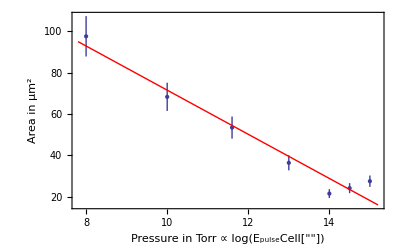

```mathematica
Show[ErrorListPlot[Transpose[{data,Table[ErrorBar[area[[i]]*0.10],{i,1,7}]}],
Frame->True,PlotStyle->Directive[PointSize[Large]],FrameLabel->{"Pressure in Torr ∝ log(E_pulseCell[""])","Area in μm^2"},FrameStyle->Directive[12]],Plot[linearFit,{x,7.8,15.2},PlotStyle->Directive[Red,Thick]]]
```